## Working with arrays

These examples demonstrate the basics of working with multidimensional arrays.

```mathematica
SetDirectory@NotebookDirectory[];
Needs["LTemplate`"]
```

```mathematica
template=
LClass["Tensor",
{
(* properties and basic argument passing *)
LFun["depth",{{Real,_}},Integer],
LFun["dimensions",{{Real,_}},{Integer,1}],
LFun["identity",{{Real,_}},{Real,_}],

(* iteration and element access *)
LFun["sum",{{Real,_}},Real],
LFun["printVector",{{Real,1}},"Void"],
LFun["printMatrix", {{Real,2}},"Void"],

(* creating Tensors of various dimensions *)
LFun["createVector",{},{Real,1}],
LFun["createMatrix",{},{Real,2}],
LFun["createCube",{},{Real,3}],
LFun["ones2345",{},{Real,4}],

LFun["zeros",{{Integer,1}},{Real,_}],
LFun["range",{Integer,Integer},{Integer,1}],
LFun["randomReal",{Integer(* n *),Real (* lower bound *), Real (* upper bound *)},{Real,1}]
}
];
```

```mathematica
CompileTemplate[template]
```

Current directory is: /Users/szhorvat/Repos/LTemplate/LTemplate/Documentation/Examples/Tensor

Unloading library Tensor ...

Generating library code ...

Compiling library code ...

/Users/szhorvat/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/Tensor.dylib

```mathematica
LoadTemplate[template]
```

```mathematica
obj=Make[Tensor]
```

Tensor[1]

We will use this random matrix for testing:

```mathematica
arr=RandomReal[1,{2,3}]
```

{{0.11704,0.466598,0.931386},{0.762592,0.0889035,0.0537262}}

Get the depth of the array:

```mathematica
obj@"depth"[arr]
```

2

Get its dimensions:

```mathematica
obj@"dimensions"[arr]
```

{2,3}

A trivial function that returns a real-valued arbitrary dimensional array as-is:

```mathematica
obj@"identity"[arr]
```

{{0.11704,0.466598,0.931386},{0.762592,0.0889035,0.0537262}}

Sum the elements of an array:

```mathematica
obj@"sum"[arr]
```

2.42025

```mathematica
Total[arr,Infinity]
```

2.42025

This function demonstrates iterating through the elements of a matrix, and printing them to the notebook:

```mathematica
obj@"printMatrix"[arr]
```

0.11704 0.466598 0.931386
 0.7625920.08890350.0537262

```mathematica
obj@"printVector"[{E,Pi,EulerGamma}]
```

1:   2.71828
   2:   3.14159
   3:  0.577216

```mathematica
MatrixForm[arr]
```

(0.11704 | 0.466598 | 0.931386
0.762592 | 0.0889035 | 0.0537262)

Create vectors, matrices or cubes (3D arrays) directly:

```mathematica
obj@"createVector"[]
```

{1.,2.,3.}

```mathematica
obj@"createMatrix"[]
```

{{1.,2.},{3.,4.}}

```mathematica
obj@"createCube"[]
```

{{{1.,2.},{3.,4.}},{{5.,6.},{7.,8.}}}

Directly create an array of ones of dimensions {2,3,4,5}.

```mathematica
obj@"ones2345"[]
```

{{{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}},{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}},{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}},{{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}},{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}},{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}}}

```mathematica
Dimensions[%]
```

{2,3,4,5}

```mathematica
obj@"zeros"[{3,2,2}]
```

{{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}},{{0.,0.},{0.,0.}}}

```mathematica
Dimensions[%]
```

{3,2,2}

Create an array of arbitrary dimensions, filled with zeros:

Create integer ranges:

```mathematica
obj@"range"[3,7]
```

{3,4,5,6,7}

```mathematica
obj@"range"[1,0]
```

{}

```mathematica
obj@"range"[1,1]
```

{1}

Generate 1000 random numbers between 0 and 10:

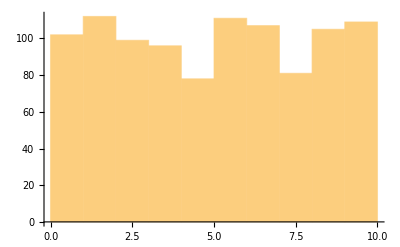

```mathematica
obj@"randomReal"[1000,0,10]//Histogram
```